## Calibrate digitized Fulton data points to an asymmetric gaussian

```mathematica
fulton={{{30,90},{3.8615494,0.892144,3.3298476}},{{90,300},{6.335588,1.026957,1.5145225}},{{300,900},{4.494302,0.6016602,1.2759474}},{{900,3000},{2.1343431,0.4564175,0.7157815}}};
logfulton={{{Log[30],Log[90]},{3.8615494,0.892144,3.3298476}},{{Log[90],Log[300]},{6.335588,1.026957,1.5145225}},{{Log[300],Log[900]},{4.494302,0.6016602,1.2759474}},{{Log[900],Log[3000]},{2.1343431,0.4564175,0.7157815}}};
```

```mathematica
"define an asymmetric Gaussian for the occurrence rate vs log-Mp distribution";
xmin=-∞;xmax=∞;
xdist=MixtureDistribution[{Limit[PDF[TruncatedDistribution[{xmin,μ},NormalDistribution[μ,σneg]],x],x->μ,Direction->"FromBelow"],Limit[PDF[TruncatedDistribution[{μ,xmax},NormalDistribution[μ,σpos]],x],x->μ,Direction->"FromAbove"]},{TruncatedDistribution[{μ,xmax},NormalDistribution[μ,σpos]],TruncatedDistribution[{xmin,μ},NormalDistribution[μ,σneg]]}];
```

```mathematica
xintegral1=Simplify[Integrate[PDF[xdist,x],{x,First[logfulton[[1]]][[1]],First[logfulton[[1]]][[2]]}],Assumptions->μ∈Reals&&σpos>0&&σneg>0]/(Log[90]-Log[30])
xintegral2=Simplify[Integrate[PDF[xdist,x],{x,First[logfulton[[2]]][[1]],First[logfulton[[2]]][[2]]}],Assumptions->μ∈Reals&&σpos>0&&σneg>0]/(Log[300]-Log[90])
xintegral3=Simplify[Integrate[PDF[xdist,x],{x,First[logfulton[[3]]][[1]],First[logfulton[[3]]][[2]]}],Assumptions->μ∈Reals&&σpos>0&&σneg>0]/(Log[900]-Log[300])
xintegral4=Simplify[Integrate[PDF[xdist,x],{x,First[logfulton[[4]]][[1]],First[logfulton[[4]]][[2]]}],Assumptions->μ∈Reals&&σpos>0&&σneg>0]/(Log[3000]-Log[900])
```

Piecewise[{{(σneg (Erf[(μ-Log[30])/(√2 σneg)]-Erf[(μ-Log[90])/(√2 σneg)]))/(σneg+σpos), μ≥Log[90]}, {(σpos (Erf[(μ-Log[30])/(√2 σpos)]-Erf[(μ-Log[90])/(√2 σpos)]))/(σneg+σpos), μ≤Log[30]}, {(σneg Erf[(μ-Log[30])/(√2 σneg)]-σpos Erf[(μ-Log[90])/(√2 σpos)])/(σneg+σpos), True}}]/(-Log[30]+Log[90])

Piecewise[{{(σneg (Erf[(μ-Log[90])/(√2 σneg)]-Erf[(μ-Log[300])/(√2 σneg)]))/(σneg+σpos), μ≥Log[300]}, {(σpos (Erf[(μ-Log[90])/(√2 σpos)]-Erf[(μ-Log[300])/(√2 σpos)]))/(σneg+σpos), μ≤Log[90]}, {(σneg Erf[(μ-Log[90])/(√2 σneg)]-σpos Erf[(μ-Log[300])/(√2 σpos)])/(σneg+σpos), True}}]/(-Log[90]+Log[300])

Piecewise[{{(σneg (Erf[(μ-Log[300])/(√2 σneg)]-Erf[(μ-Log[900])/(√2 σneg)]))/(σneg+σpos), μ≥Log[900]}, {(σpos (Erf[(μ-Log[300])/(√2 σpos)]-Erf[(μ-Log[900])/(√2 σpos)]))/(σneg+σpos), μ≤Log[300]}, {(σneg Erf[(μ-Log[300])/(√2 σneg)]-σpos Erf[(μ-Log[900])/(√2 σpos)])/(σneg+σpos), True}}]/(-Log[300]+Log[900])

Piecewise[{{(σneg (Erf[(μ-Log[900])/(√2 σneg)]-Erf[(μ-Log[3000])/(√2 σneg)]))/(σneg+σpos), μ≥Log[3000]}, {(σpos (Erf[(μ-Log[900])/(√2 σpos)]-Erf[(μ-Log[3000])/(√2 σpos)]))/(σneg+σpos), μ≤Log[900]}, {(σneg Erf[(μ-Log[900])/(√2 σneg)]-σpos Erf[(μ-Log[3000])/(√2 σpos)])/(σneg+σpos), True}}]/(-Log[900]+Log[3000])

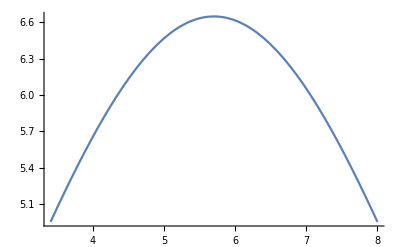

5.58464

6.47478

6.50337

5.63645

```mathematica
"example approaching a uniform spread";
Plot[f PDF[xdist,x]/.f->50/.μ->Log[300]/.σpos->σneg/.σneg->3,{x,Log[30],Log[3000]},PlotRange->{All,{0,All}}]
N[f xintegral1/.μ->Log[300]/.σpos->σneg/.σneg->3/.f->50]
N[f xintegral2/.μ->Log[300]/.σpos->σneg/.σneg->3/.f->50]
N[f xintegral3/.μ->Log[300]/.σpos->σneg/.σneg->3/.f->50]
N[f xintegral4/.μ->Log[300]/.σpos->σneg/.σneg->3/.f->50]
```

```mathematica
"define an asymmetric Gaussian for the indivual error measurements";
ymin=0;ymax=∞;
μ1=Last[logfulton[[1]]][[1]];
σneg1=Last[logfulton[[1]]][[2]];
σpos1=Last[logfulton[[1]]][[3]];
"data point 1, 30-90 Earth masses";
ydist1=MixtureDistribution[{Limit[PDF[TruncatedDistribution[{ymin,μ1},NormalDistribution[μ1,σneg1]],x],x->μ1,Direction->"FromBelow"],Limit[PDF[TruncatedDistribution[{μ1,ymax},NormalDistribution[μ1,σpos1]],x],x->μ1,Direction->"FromAbove"]},{TruncatedDistribution[{μ1,ymax},NormalDistribution[μ1,σpos1]],TruncatedDistribution[{ymin,μ1},NormalDistribution[μ1,σneg1]]}];
"data point 2, 90-300 Earth masses";
μ2=Last[logfulton[[2]]][[1]];
σneg2=Last[logfulton[[2]]][[2]];
σpos2=Last[logfulton[[2]]][[3]];
ydist2=MixtureDistribution[{Limit[PDF[TruncatedDistribution[{ymin,μ2},NormalDistribution[μ2,σneg2]],x],x->μ2,Direction->"FromBelow"],Limit[PDF[TruncatedDistribution[{μ2,ymax},NormalDistribution[μ2,σpos2]],x],x->μ2,Direction->"FromAbove"]},{TruncatedDistribution[{μ2,ymax},NormalDistribution[μ2,σpos2]],TruncatedDistribution[{ymin,μ2},NormalDistribution[μ2,σneg2]]}];
"data point 3, 300-900 Earth masses";
μ3=Last[logfulton[[3]]][[1]];
σneg3=Last[logfulton[[3]]][[2]];
σpos3=Last[logfulton[[3]]][[3]];
ydist3=MixtureDistribution[{Limit[PDF[TruncatedDistribution[{ymin,μ3},NormalDistribution[μ3,σneg3]],x],x->μ3,Direction->"FromBelow"],Limit[PDF[TruncatedDistribution[{μ3,ymax},NormalDistribution[μ3,σpos3]],x],x->μ3,Direction->"FromAbove"]},{TruncatedDistribution[{μ3,ymax},NormalDistribution[μ3,σpos3]],TruncatedDistribution[{ymin,μ3},NormalDistribution[μ3,σneg3]]}];
"data point 4, 900-3000 Earth masses";
μ4=Last[logfulton[[4]]][[1]];
σneg4=Last[logfulton[[4]]][[2]];
σpos4=Last[logfulton[[4]]][[3]];
ydist4=MixtureDistribution[{Limit[PDF[TruncatedDistribution[{ymin,μ4},NormalDistribution[μ4,σneg4]],x],x->μ4,Direction->"FromBelow"],Limit[PDF[TruncatedDistribution[{μ4,ymax},NormalDistribution[μ4,σpos4]],x],x->μ4,Direction->"FromAbove"]},{TruncatedDistribution[{μ4,ymax},NormalDistribution[μ4,σpos4]],TruncatedDistribution[{ymin,μ4},NormalDistribution[μ4,σneg4]]}];
```

```mathematica
loglike=LogLikelihood[ydist1,{f xintegral1}]+LogLikelihood[ydist2,{f xintegral2}]+LogLikelihood[ydist3,{f xintegral3}]+LogLikelihood[ydist4,{f xintegral4}]
```

(Piecewise[{{Log[0.188984 ⅇ^(-0.628203 (-3.86155+(f σneg (Erf[(μ-Log[30])/(√2 σneg)]-Erf[(μ-Log[90])/(√2 σneg)]))/((σneg+σpos) (-Log[30]+Log[90])))^2)], 0<(f σneg Erf[(μ-Log[30])/(√2 σneg)])/((σneg+σpos) (-Log[30]+Log[90]))-(f σneg Erf[(μ-Log[90])/(√2 σneg)])/((σneg+σpos) (-Log[30]+Log[90]))≤3.86155&&μ≥Log[90]}, {Log[0.188984 ⅇ^(-0.628203 (-3.86155+(f σpos (Erf[(μ-Log[30])/(√2 σpos)]-Erf[(μ-Log[90])/(√2 σpos)]))/((σneg+σpos) (-Log[30]+Log[90])))^2)], μ≤Log[30]&&0<(f σpos Erf[(μ-Log[30])/(√2 σpos)])/((σneg+σpos) (-Log[30]+Log[90]))-(f σpos Erf[(μ-Log[90])/(√2 σpos)])/((σneg+σpos) (-Log[30]+Log[90]))≤3.86155}, {Log[0.188984 ⅇ^(-0.628203 (-3.86155+(f (σneg Erf[(μ-Log[30])/(√2 σneg)]-σpos Erf[(μ-Log[90])/(√2 σpos)]))/((σneg+σpos) (-Log[30]+Log[90])))^2)], (0<(f σneg Erf[(μ-Log[30])/(√2 σneg)])/((σneg+σpos) (-Log[30]+Log[90]))-(f σneg Erf[(μ-Log[90])/(√2 σneg)])/((σneg+σpos) (-Log[30]+Log[90]))≤3.86155&&μ≥Log[90])||(μ≤Log[30]&&0<(f σpos Erf[(μ-Log[30])/(√2 σpos)])/((σneg+σpos) (-Log[30]+Log[90]))-(f σpos Erf[(μ-Log[90])/(√2 σpos)])/((σneg+σpos) (-Log[30]+Log[90]))≤3.86155)||(Log[30]<μ<Log[90]&&0<(f σneg Erf[(μ-Log[30])/(√2 σneg)])/((σneg+σpos) (-Log[30]+Log[90]))-(f σpos Erf[(μ-Log[90])/(√2 σpos)])/((σneg+σpos) (-Log[30]+Log[90]))≤3.86155)}, {Log[0.188984 ⅇ^(-0.0450943 (-3.86155+(f σneg (Erf[(μ-Log[30])/(√2 σneg)]-Erf[(μ-Log[90])/(√2 σneg)]))/((σneg+σpos) (-Log[30]+Log[90])))^2)], μ≥Log[90]&&(f σneg Erf[(μ-Log[30])/(√2 σneg)])/((σneg+σpos) (-Log[30]+Log[90]))-(f σneg Erf[(μ-Log[90])/(√2 σneg)])/((σneg+σpos) (-Log[30]+Log[90]))>3.86155}, {Log[0.188984 ⅇ^(-0.0450943 (-3.86155+(f σpos (Erf[(μ-Log[30])/(√2 σpos)]-Erf[(μ-Log[90])/(√2 σpos)]))/((σneg+σpos) (-Log[30]+Log[90])))^2)], μ≤Log[30]&&(f σpos Erf[(μ-Log[30])/(√2 σpos)])/((σneg+σpos) (-Log[30]+Log[90]))-(f σpos Erf[(μ-Log[90])/(√2 σpos)])/((σneg+σpos) (-Log[30]+Log[90]))>3.86155}, {Log[0.188984 ⅇ^(-0.0450943 (-3.86155+(f (σneg Erf[(μ-Log[30])/(√2 σneg)]-σpos Erf[(μ-Log[90])/(√2 σpos)]))/((σneg+σpos) (-Log[30]+Log[90])))^2)], (μ≤Log[30]&&(f σpos Erf[(μ-Log[30])/(√2 σpos)])/((σneg+σpos) (-Log[30]+Log[90]))-(f σpos Erf[(μ-Log[90])/(√2 σpos)])/((σneg+σpos) (-Log[30]+Log[90]))>3.86155)||(Log[30]<μ<Log[90]&&(f σneg Erf[(μ-Log[30])/(√2 σneg)])/((σneg+σpos) (-Log[30]+Log[90]))-(f σpos Erf[(μ-Log[90])/(√2 σpos)])/((σneg+σpos) (-Log[30]+Log[90]))>3.86155)||(μ≥Log[90]&&(f σneg Erf[(μ-Log[30])/(√2 σneg)])/((σneg+σpos) (-Log[30]+Log[90]))-(f σneg Erf[(μ-Log[90])/(√2 σneg)])/((σneg+σpos) (-Log[30]+Log[90]))>3.86155)}, {-∞, True}}])+(Piecewise[{{Log[0.313945 ⅇ^(-0.474095 (-6.33559+(f σneg (Erf[(μ-Log[90])/(√2 σneg)]-Erf[(μ-Log[300])/(√2 σneg)]))/((σneg+σpos) (-Log[90]+Log[300])))^2)], 0<(f σneg Erf[(μ-Log[90])/(√2 σneg)])/((σneg+σpos) (-Log[90]+Log[300]))-(f σneg Erf[(μ-Log[300])/(√2 σneg)])/((σneg+σpos) (-Log[90]+Log[300]))≤6.33559&&μ≥Log[300]}, {Log[0.313945 ⅇ^(-0.474095 (-6.33559+(f σpos (Erf[(μ-Log[90])/(√2 σpos)]-Erf[(μ-Log[300])/(√2 σpos)]))/((σneg+σpos) (-Log[90]+Log[300])))^2)], μ≤Log[90]&&0<(f σpos Erf[(μ-Log[90])/(√2 σpos)])/((σneg+σpos) (-Log[90]+Log[300]))-(f σpos Erf[(μ-Log[300])/(√2 σpos)])/((σneg+σpos) (-Log[90]+Log[300]))≤6.33559}, {Log[0.313945 ⅇ^(-0.474095 (-6.33559+(f (σneg Erf[(μ-Log[90])/(√2 σneg)]-σpos Erf[(μ-Log[300])/(√2 σpos)]))/((σneg+σpos) (-Log[90]+Log[300])))^2)], (0<(f σneg Erf[(μ-Log[90])/(√2 σneg)])/((σneg+σpos) (-Log[90]+Log[300]))-(f σneg Erf[(μ-Log[300])/(√2 σneg)])/((σneg+σpos) (-Log[90]+Log[300]))≤6.33559&&μ≥Log[300])||(μ≤Log[90]&&0<(f σpos Erf[(μ-Log[90])/(√2 σpos)])/((σneg+σpos) (-Log[90]+Log[300]))-(f σpos Erf[(μ-Log[300])/(√2 σpos)])/((σneg+σpos) (-Log[90]+Log[300]))≤6.33559)||(Log[90]<μ<Log[300]&&0<(f σneg Erf[(μ-Log[90])/(√2 σneg)])/((σneg+σpos) (-Log[90]+Log[300]))-(f σpos Erf[(μ-Log[300])/(√2 σpos)])/((σneg+σpos) (-Log[90]+Log[300]))≤6.33559)}, {Log[0.313945 ⅇ^(-0.217981 (-6.33559+(f σneg (Erf[(μ-Log[90])/(√2 σneg)]-Erf[(μ-Log[300])/(√2 σneg)]))/((σneg+σpos) (-Log[90]+Log[300])))^2)], μ≥Log[300]&&(f σneg Erf[(μ-Log[90])/(√2 σneg)])/((σneg+σpos) (-Log[90]+Log[300]))-(f σneg Erf[(μ-Log[300])/(√2 σneg)])/((σneg+σpos) (-Log[90]+Log[300]))>6.33559}, {Log[0.313945 ⅇ^(-0.217981 (-6.33559+(f σpos (Erf[(μ-Log[90])/(√2 σpos)]-Erf[(μ-Log[300])/(√2 σpos)]))/((σneg+σpos) (-Log[90]+Log[300])))^2)], μ≤Log[90]&&(f σpos Erf[(μ-Log[90])/(√2 σpos)])/((σneg+σpos) (-Log[90]+Log[300]))-(f σpos Erf[(μ-Log[300])/(√2 σpos)])/((σneg+σpos) (-Log[90]+Log[300]))>6.33559}, {Log[0.313945 ⅇ^(-0.217981 (-6.33559+(f (σneg Erf[(μ-Log[90])/(√2 σneg)]-σpos Erf[(μ-Log[300])/(√2 σpos)]))/((σneg+σpos) (-Log[90]+Log[300])))^2)], (μ≤Log[90]&&(f σpos Erf[(μ-Log[90])/(√2 σpos)])/((σneg+σpos) (-Log[90]+Log[300]))-(f σpos Erf[(μ-Log[300])/(√2 σpos)])/((σneg+σpos) (-Log[90]+Log[300]))>6.33559)||(Log[90]<μ<Log[300]&&(f σneg Erf[(μ-Log[90])/(√2 σneg)])/((σneg+σpos) (-Log[90]+Log[300]))-(f σpos Erf[(μ-Log[300])/(√2 σpos)])/((σneg+σpos) (-Log[90]+Log[300]))>6.33559)||(μ≥Log[300]&&(f σneg Erf[(μ-Log[90])/(√2 σneg)])/((σneg+σpos) (-Log[90]+Log[300]))-(f σneg Erf[(μ-Log[300])/(√2 σneg)])/((σneg+σpos) (-Log[90]+Log[300]))>6.33559)}, {-∞, True}}])+(Piecewise[{{Log[0.424947 ⅇ^(-1.38123 (-4.4943+(f σneg (Erf[(μ-Log[300])/(√2 σneg)]-Erf[(μ-Log[900])/(√2 σneg)]))/((σneg+σpos) (-Log[300]+Log[900])))^2)], 0<(f σneg Erf[(μ-Log[300])/(√2 σneg)])/((σneg+σpos) (-Log[300]+Log[900]))-(f σneg Erf[(μ-Log[900])/(√2 σneg)])/((σneg+σpos) (-Log[300]+Log[900]))≤4.4943&&μ≥Log[900]}, {Log[0.424947 ⅇ^(-1.38123 (-4.4943+(f σpos (Erf[(μ-Log[300])/(√2 σpos)]-Erf[(μ-Log[900])/(√2 σpos)]))/((σneg+σpos) (-Log[300]+Log[900])))^2)], μ≤Log[300]&&0<(f σpos Erf[(μ-Log[300])/(√2 σpos)])/((σneg+σpos) (-Log[300]+Log[900]))-(f σpos Erf[(μ-Log[900])/(√2 σpos)])/((σneg+σpos) (-Log[300]+Log[900]))≤4.4943}, {Log[0.424947 ⅇ^(-1.38123 (-4.4943+(f (σneg Erf[(μ-Log[300])/(√2 σneg)]-σpos Erf[(μ-Log[900])/(√2 σpos)]))/((σneg+σpos) (-Log[300]+Log[900])))^2)], (0<(f σneg Erf[(μ-Log[300])/(√2 σneg)])/((σneg+σpos) (-Log[300]+Log[900]))-(f σneg Erf[(μ-Log[900])/(√2 σneg)])/((σneg+σpos) (-Log[300]+Log[900]))≤4.4943&&μ≥Log[900])||(μ≤Log[300]&&0<(f σpos Erf[(μ-Log[300])/(√2 σpos)])/((σneg+σpos) (-Log[300]+Log[900]))-(f σpos Erf[(μ-Log[900])/(√2 σpos)])/((σneg+σpos) (-Log[300]+Log[900]))≤4.4943)||(Log[300]<μ<Log[900]&&0<(f σneg Erf[(μ-Log[300])/(√2 σneg)])/((σneg+σpos) (-Log[300]+Log[900]))-(f σpos Erf[(μ-Log[900])/(√2 σpos)])/((σneg+σpos) (-Log[300]+Log[900]))≤4.4943)}, {Log[0.424947 ⅇ^(-0.307117 (-4.4943+(f σneg (Erf[(μ-Log[300])/(√2 σneg)]-Erf[(μ-Log[900])/(√2 σneg)]))/((σneg+σpos) (-Log[300]+Log[900])))^2)], μ≥Log[900]&&(f σneg Erf[(μ-Log[300])/(√2 σneg)])/((σneg+σpos) (-Log[300]+Log[900]))-(f σneg Erf[(μ-Log[900])/(√2 σneg)])/((σneg+σpos) (-Log[300]+Log[900]))>4.4943}, {Log[0.424947 ⅇ^(-0.307117 (-4.4943+(f σpos (Erf[(μ-Log[300])/(√2 σpos)]-Erf[(μ-Log[900])/(√2 σpos)]))/((σneg+σpos) (-Log[300]+Log[900])))^2)], μ≤Log[300]&&(f σpos Erf[(μ-Log[300])/(√2 σpos)])/((σneg+σpos) (-Log[300]+Log[900]))-(f σpos Erf[(μ-Log[900])/(√2 σpos)])/((σneg+σpos) (-Log[300]+Log[900]))>4.4943}, {Log[0.424947 ⅇ^(-0.307117 (-4.4943+(f (σneg Erf[(μ-Log[300])/(√2 σneg)]-σpos Erf[(μ-Log[900])/(√2 σpos)]))/((σneg+σpos) (-Log[300]+Log[900])))^2)], (μ≤Log[300]&&(f σpos Erf[(μ-Log[300])/(√2 σpos)])/((σneg+σpos) (-Log[300]+Log[900]))-(f σpos Erf[(μ-Log[900])/(√2 σpos)])/((σneg+σpos) (-Log[300]+Log[900]))>4.4943)||(Log[300]<μ<Log[900]&&(f σneg Erf[(μ-Log[300])/(√2 σneg)])/((σneg+σpos) (-Log[300]+Log[900]))-(f σpos Erf[(μ-Log[900])/(√2 σpos)])/((σneg+σpos) (-Log[300]+Log[900]))>4.4943)||(μ≥Log[900]&&(f σneg Erf[(μ-Log[300])/(√2 σneg)])/((σneg+σpos) (-Log[300]+Log[900]))-(f σneg Erf[(μ-Log[900])/(√2 σneg)])/((σneg+σpos) (-Log[300]+Log[900]))>4.4943)}, {-∞, True}}])+(Piecewise[{{Log[0.680674 ⅇ^(-2.40019 (-2.13434+(f σneg (Erf[(μ-Log[900])/(√2 σneg)]-Erf[(μ-Log[3000])/(√2 σneg)]))/((σneg+σpos) (-Log[900]+Log[3000])))^2)], 0<(f σneg Erf[(μ-Log[900])/(√2 σneg)])/((σneg+σpos) (-Log[900]+Log[3000]))-(f σneg Erf[(μ-Log[3000])/(√2 σneg)])/((σneg+σpos) (-Log[900]+Log[3000]))≤2.13434&&μ≥Log[3000]}, {Log[0.680674 ⅇ^(-2.40019 (-2.13434+(f σpos (Erf[(μ-Log[900])/(√2 σpos)]-Erf[(μ-Log[3000])/(√2 σpos)]))/((σneg+σpos) (-Log[900]+Log[3000])))^2)], μ≤Log[900]&&0<(f σpos Erf[(μ-Log[900])/(√2 σpos)])/((σneg+σpos) (-Log[900]+Log[3000]))-(f σpos Erf[(μ-Log[3000])/(√2 σpos)])/((σneg+σpos) (-Log[900]+Log[3000]))≤2.13434}, {Log[0.680674 ⅇ^(-2.40019 (-2.13434+(f (σneg Erf[(μ-Log[900])/(√2 σneg)]-σpos Erf[(μ-Log[3000])/(√2 σpos)]))/((σneg+σpos) (-Log[900]+Log[3000])))^2)], (0<(f σneg Erf[(μ-Log[900])/(√2 σneg)])/((σneg+σpos) (-Log[900]+Log[3000]))-(f σneg Erf[(μ-Log[3000])/(√2 σneg)])/((σneg+σpos) (-Log[900]+Log[3000]))≤2.13434&&μ≥Log[3000])||(μ≤Log[900]&&0<(f σpos Erf[(μ-Log[900])/(√2 σpos)])/((σneg+σpos) (-Log[900]+Log[3000]))-(f σpos Erf[(μ-Log[3000])/(√2 σpos)])/((σneg+σpos) (-Log[900]+Log[3000]))≤2.13434)||(Log[900]<μ<Log[3000]&&0<(f σneg Erf[(μ-Log[900])/(√2 σneg)])/((σneg+σpos) (-Log[900]+Log[3000]))-(f σpos Erf[(μ-Log[3000])/(√2 σpos)])/((σneg+σpos) (-Log[900]+Log[3000]))≤2.13434)}, {Log[0.680674 ⅇ^(-0.975908 (-2.13434+(f σneg (Erf[(μ-Log[900])/(√2 σneg)]-Erf[(μ-Log[3000])/(√2 σneg)]))/((σneg+σpos) (-Log[900]+Log[3000])))^2)], μ≥Log[3000]&&(f σneg Erf[(μ-Log[900])/(√2 σneg)])/((σneg+σpos) (-Log[900]+Log[3000]))-(f σneg Erf[(μ-Log[3000])/(√2 σneg)])/((σneg+σpos) (-Log[900]+Log[3000]))>2.13434}, {Log[0.680674 ⅇ^(-0.975908 (-2.13434+(f σpos (Erf[(μ-Log[900])/(√2 σpos)]-Erf[(μ-Log[3000])/(√2 σpos)]))/((σneg+σpos) (-Log[900]+Log[3000])))^2)], μ≤Log[900]&&(f σpos Erf[(μ-Log[900])/(√2 σpos)])/((σneg+σpos) (-Log[900]+Log[3000]))-(f σpos Erf[(μ-Log[3000])/(√2 σpos)])/((σneg+σpos) (-Log[900]+Log[3000]))>2.13434}, {Log[0.680674 ⅇ^(-0.975908 (-2.13434+(f (σneg Erf[(μ-Log[900])/(√2 σneg)]-σpos Erf[(μ-Log[3000])/(√2 σpos)]))/((σneg+σpos) (-Log[900]+Log[3000])))^2)], (μ≤Log[900]&&(f σpos Erf[(μ-Log[900])/(√2 σpos)])/((σneg+σpos) (-Log[900]+Log[3000]))-(f σpos Erf[(μ-Log[3000])/(√2 σpos)])/((σneg+σpos) (-Log[900]+Log[3000]))>2.13434)||(Log[900]<μ<Log[3000]&&(f σneg Erf[(μ-Log[900])/(√2 σneg)])/((σneg+σpos) (-Log[900]+Log[3000]))-(f σpos Erf[(μ-Log[3000])/(√2 σpos)])/((σneg+σpos) (-Log[900]+Log[3000]))>2.13434)||(μ≥Log[3000]&&(f σneg Erf[(μ-Log[900])/(√2 σneg)])/((σneg+σpos) (-Log[900]+Log[3000]))-(f σneg Erf[(μ-Log[3000])/(√2 σneg)])/((σneg+σpos) (-Log[900]+Log[3000]))>2.13434)}, {-∞, True}}])

```mathematica
loglike/.σpos->σneg/.σneg->10/.f->100/.μ->Log[300]
loglike/.σpos->σneg/.σneg->3/.f->50/.μ->Log[300]
```

-10.2059

-17.4121

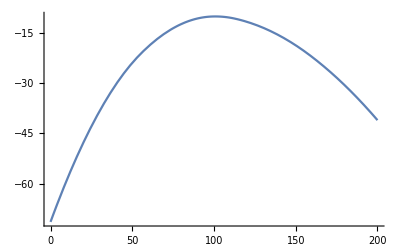

{-10.2029,{f→100.814}}

```mathematica
ftrial=10;μtrial=Log[300];σnegtrial=10;σpostrial=10;
Plot[loglike/.σpos->σneg/.σneg->10/.μ->Log[300],{f,0,200}]
NMaximize[{loglike/.σpos->σneg/.σneg->10/.μ->Log[300],0<f<200},f]
```

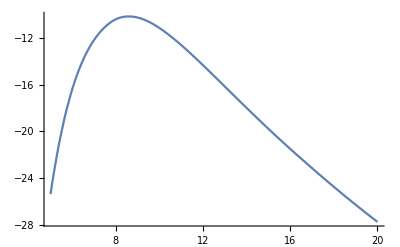

{-10.1402,{σ→8.58883}}

```mathematica
ftrial=87.32002147739244;μtrial=Log[300];σnegtrial=10;σpostrial=10;
Plot[loglike/.f->ftrial/.μ->μtrial/.σpos->σneg/.σneg->σ,{σ,5,20}]
NMaximize[{loglike/.f->ftrial/.μ->μtrial/.σpos->σneg/.σneg->σ,5<σ<20},σ]
```

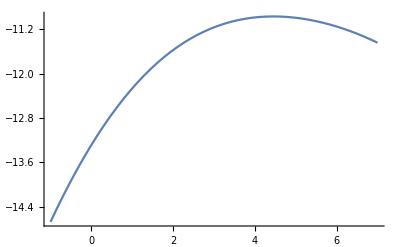

{-10.9664,{μ→4.45407}}

```mathematica
ftrial=87.32002147739244;μtrial=Log[300];σnegtrial=9.961400056571682;σpostrial=9.961400056571682;
Plot[loglike/.f->ftrial/.σpos->σnegtrial/.σneg->σpostrial,{μ,-1,7}]
NMaximize[{loglike/.f->ftrial/.σpos->σnegtrial/.σneg->σpostrial,-1<μ<7},μ]
```

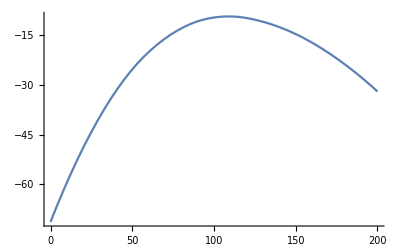

{-10.2029,{f→100.814}}

```mathematica
ftrial=87.32002147739244;μtrial=2.5165978211606665;σnegtrial=9.961400056571682;σpostrial=9.961400056571682;
Plot[loglike/.σpos->σneg/.σneg->σnegtrial/.μ->μtrial,{f,0,200}]
NMaximize[{loglike/.σpos->σneg/.σneg->10/.μ->Log[300],0<f<200},f]
```

```mathematica
FindMaximum[{loglike/.σpos->σneg,σneg>0,Log[30]<μ<Log[3000]},{{σneg,σnegtrial},{μ,μtrial},{f,ftrial}}]
```

FindMaximum::nrnum: The function value ∞ is not a real number at {σneg,μ,f} = {0.0263141,7.08758,-6.67446}.

{-4.1274,{σneg→1.49512,μ→5.14901,f→23.825}}

```mathematica
FindMaximum[{loglike,σpos>0.1,σneg>0.1,Log[30]<μ<Log[3000]},{{σpos,σnegtrial},{σneg,σnegtrial},{μ,μtrial},{f,ftrial}}]
```

{-4.06509,{σpos→1.79056,σneg→0.697248,μ→4.67821,f→20.7062}}

```mathematica
fbest=20.706237623948798;
σposbest=1.7905555279832017;
σnegbest=0.6972478014498614;
μbest=4.678213692386503;
```

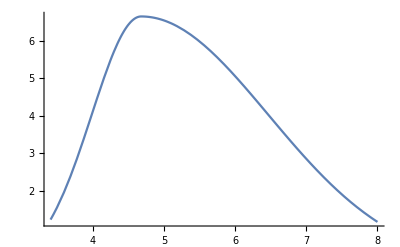

{3.86155,{3.86155,0.892144,3.32985}}

{6.33559,{6.33559,1.02696,1.51452}}

{4.4943,{4.4943,0.60166,1.27595}}

{2.13434,{2.13434,0.456418,0.715782}}

```mathematica
Plot[f PDF[xdist,x]/.f->fbest/.μ->μbest/.σpos->σposbest/.σneg->σnegbest,{x,Log[30],Log[3000]},PlotRange->{All,{0,All}}]
{N[f xintegral1/.f->fbest/.μ->μbest/.σpos->σposbest/.σneg->σnegbest],Last[logfulton[[1]]]}
{N[f xintegral2/.f->fbest/.μ->μbest/.σpos->σposbest/.σneg->σnegbest],Last[logfulton[[2]]]}
{N[f xintegral3/.f->fbest/.μ->μbest/.σpos->σposbest/.σneg->σnegbest],Last[logfulton[[3]]]}
{N[f xintegral4/.f->fbest/.μ->μbest/.σpos->σposbest/.σneg->σnegbest],Last[logfulton[[4]]]}
```

## Works great! Here is plotted better...

```mathematica
fultonplot=Table[{Around[N[Mean[First[logfulton[[i]]]]],Mean[First[logfulton[[i]]]]-First[First[logfulton[[i]]]]],Around[Last[logfulton[[i]]][[1]],{Last[logfulton[[i]]][[2]],Last[logfulton[[i]]][[3]]}]},{i,1,Length[logfulton]}]
fitplot={{fultonplot[[1,1]][[1]],f xintegral1/.f->fbest/.μ->μbest/.σpos->σposbest/.σneg->σnegbest},{fultonplot[[2,1]][[1]],f xintegral2/.f->fbest/.μ->μbest/.σpos->σposbest/.σneg->σnegbest},{fultonplot[[3,1]][[1]],f xintegral3/.f->fbest/.μ->μbest/.σpos->σposbest/.σneg->σnegbest},{fultonplot[[4,1]][[1]],f xintegral4/.f->fbest/.μ->μbest/.σpos->σposbest/.σneg->σnegbest}}
```

{{4.00.5,3.90.93.3},{5.10.6,6.31.01.5},{6.30.5,4.50.61.3},{7.40.6,2.10.50.7}}

{{3.9505,3.86155},{5.1018,6.33559},{6.25309,4.4943},{7.40438,2.13434}}

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

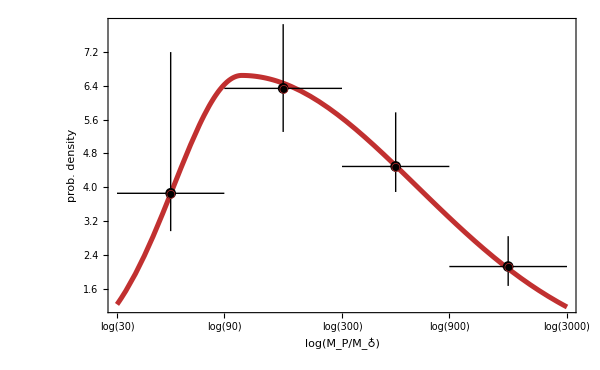

```mathematica
xticks={{Log[30],"log(30)"},{Log[90],"log(90)"},{Log[300],"log(300)"},{Log[900],"log(900)"},{Log[3000],"log(3000)"}};
<<ErrorBarPlots`
finalplot=
Show[Plot[f PDF[xdist,x]/.f->fbest/.μ->μbest/.σpos->σposbest/.σneg->σnegbest,{x,Log[30],Log[3000]},PlotRange->{{Log[30],Log[3000]},{0,All}},Frame->True,FrameTicks->{Automatic,{xticks,None}},FrameLabel->{"log(M_P/M_♁)","prob. density"},ImageSize->{600,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->26},PlotStyle->Directive[ColorData["CherryTones"][0.3],Thickness[0.006]]],ListPlot[fultonplot,PlotStyle->Black],ListPlot[fitplot,PlotMarkers->"○",PlotStyle->ColorData["CherryTones"][0.3]]]
```

## Now convert to radii

```mathematica
"define an asymmetric Gaussian for the occurrence rate vs log-Mp distribution";
xmin=-∞;xmax=∞;
xdist=MixtureDistribution[{Limit[PDF[TruncatedDistribution[{xmin,μ},NormalDistribution[μ,σneg]],x],x->μ,Direction->"FromBelow"],Limit[PDF[TruncatedDistribution[{μ,xmax},NormalDistribution[μ,σpos]],x],x->μ,Direction->"FromAbove"]},{TruncatedDistribution[{μ,xmax},NormalDistribution[μ,σpos]],TruncatedDistribution[{xmin,μ},NormalDistribution[μ,σneg]]}];
```

```mathematica
fbest=20.706237623948798;
σposbest=1.7905555279832017;
σnegbest=0.6972478014498614;
μbest=4.678213692386503;
```

```mathematica
Plot[f PDF[xdist,x]/.f->fbest/.μ->μbest/.σpos->σposbest/.σneg->σnegbest,{x,Log[30],Log[3000]},PlotRange->{All,{0,All}}]
```

-Graphics-

```mathematica
Integrate[PDF[xdist,x]/.μ->μbest/.σpos->σposbest/.σneg->σnegbest,{x,-∞,∞}]
```

1.

```mathematica
100Integrate[PDF[xdist,x]/.μ->μbest/.σpos->σposbest/.σneg->σnegbest,{x,-∞,Log[10]}]
```

0.018398

```mathematica
Exp[RandomVariate[xdist/.μ->μbest/.σpos->σposbest/.σneg->σnegbest]]
```

45.4558

```mathematica
chenpost=Import[StringJoin[NotebookDirectory[],"fitting_parameters.h5"],"Data"][[1]];
```

```mathematica
Dimensions[chenpost]
```

{1020431,12}

```mathematica
Median[chenpost]
```

{0.00347887,0.278957,0.586262,-0.0434196,0.88025,0.0395285,0.145714,0.0736781,0.0438694,0.314028,2.12304,4.42574}

```mathematica
C1post=chenpost[[All,1]];
S1post=chenpost[[All,2]];
S2post=chenpost[[All,3]];
S3post=chenpost[[All,4]];
S4post=chenpost[[All,5]];
σ1post=chenpost[[All,6]];
σ2post=chenpost[[All,7]];
σ3post=chenpost[[All,8]];
σ4post=chenpost[[All,9]];
T0=-4;
T1post=chenpost[[All,10]];
T2post=chenpost[[All,11]];
T3post=chenpost[[All,12]];
T4=6;
C2[C1_,S1_,S2_,T1_]:=C1+(S1-S2)T1
C3[C2_,S2_,S3_,T2_]:=C2+(S2-S3)T2
C4[C3_,S3_,S4_,T3_]:=C3+(S3-S4)T3
```

```mathematica
log10R[C1_,S1_,S2_,S3_,S4_,σR1_,σR2_,σR3_,σR4_,T1_,T2_,T3_,log10M_]:=Piecewise[{{RandomVariate[NormalDistribution[C1+log10M*S1,σR1]],T0<log10M<T1},{RandomVariate[NormalDistribution[C2[C1,S1,S2,T1]+log10M*S2,σR2]],T1<log10M<T2},{RandomVariate[NormalDistribution[C3[C2[C1,S1,S2,T1],S2,S3,T2]+log10M*S3,σR3]],T2<log10M<T3},{RandomVariate[NormalDistribution[C4[C3[C2[C1,S1,S2,T1],S2,S3,T2],S3,S4,T3]+log10M*S4,σR4]],T3<log10M<T4}}];
```

```mathematica
Clear[j]
j=1
```

1

```mathematica
10^log10R[C1post[[j]],S1post[[j]],S2post[[j]],S3post[[j]],S4post[[j]],σ1post[[j]],σ2post[[j]],σ3post[[j]],σ4post[[j]],T1post[[j]],T2post[[j]],T3post[[j]],Log10[1]]
```

1.27418

```mathematica
fultonmasses=Log10[Exp[RandomVariate[xdist/.μ->μbest/.σpos->σposbest/.σneg->σnegbest,1500000]]];
fultonmasses=Select[fultonmasses,#<Log10[14*317.907]&];
Length[fultonmasses]
```

1459161

```mathematica
k=0;Label[kloop];k=k+1;j=RandomChoice[Range[Length[chenpost]]];Subscript[Rdraw, k]=10^log10R[C1post[[j]],S1post[[j]],S2post[[j]],S3post[[j]],S4post[[j]],σ1post[[j]],σ2post[[j]],σ3post[[j]],σ4post[[j]],T1post[[j]],T2post[[j]],T3post[[j]],RandomChoice[fultonmasses]];If[k<1200000,Goto[kloop]];
```

```mathematica
Rmin=0.09466132170542056;
Rmax=18.932264341084124;
```

```mathematica
Rdraws=Select[Table[Subscript[Rdraw, kk],{kk,1,1200000}],Rmin<#<Rmax&];
Length[Rdraws]
```

1156220

```mathematica
Length[Rdraws[[1;;1000000]]]
```

1000000

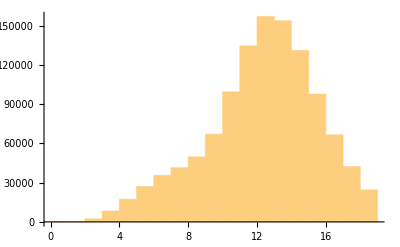

```mathematica
Histogram[Rdraws]
```

```mathematica
Export[StringJoin[NotebookDirectory[],"fulton_Rsims.dat"],Rdraws[[1;;1000000]],"Table"]
```